```mathematica
Limit[Assuming[{p∈Reals,a∈Reals,a>0},Integrate[r Sinc[p r]Exp[-a r],{r,0,∞}]],a->0]
```

1/p^2

```mathematica
Assuming[{p∈Reals,a∈Reals,a>0},Integrate[r^3 Sinc[p r]Exp[-a r],{r,0,∞}]]
```

-(2 (-3 a^2+p^2))/((a^2+p^2)^3)

```mathematica
Assuming[{p∈Reals,a∈Reals,a>0},Integrate[Sinc[p r](2 (-3 a^2+p^2))/((a^2+p^2)^3),{p,0,∞}]]
```

ConditionalExpression[(ⅇ^(-a Abs[r]) π (6-6 ⅇ^(a Abs[r])+a^2 r^2+4 a Abs[r]))/(2 a^4 Abs[r]),r∈Reals]

```mathematica
ImVs[a1_,mD_,σ_]:=Block[{a=a1,temp= π 0.155 0.2^2 σ^2 Quiet[NIntegrate[1/(p^3 (p^2+mD^2)^2) Sinc[0],{p,a,∞}]]},Interpolation[ParallelTable[{r,π 0.155 0.2^2 σ^2 Quiet[NIntegrate[1/(p^3 (p^2+mD^2)^2) Sinc[p r],{p,a,∞}]]-temp},{r,0,50,1/10}]]];
```

```mathematica
ReVsm0[a1_,mD_,σ_]:=Block[{a=a1,temp=1/(2 π^2)Quiet[NIntegrate[1/p^4 Sinc[0],{p,a,∞}]]},Interpolation[ParallelTable[{r,1/(2 π^2) Quiet[NIntegrate[1/p^4 Sinc[p r],{p,a,∞}]]-temp},{r,0,50,1/10}]]];
```

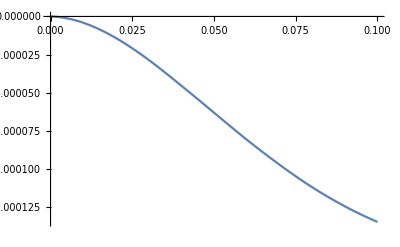

```mathematica
ReVsInter=Quiet[ReVsm0[5,0.2,0.17]];
Plot[ReVsInter[x/0.197],{x,0,0.1},PlotRange->All]
```

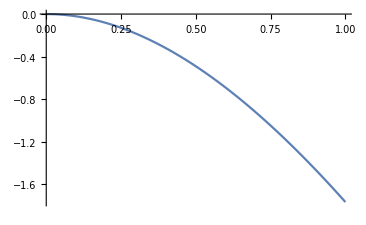

```mathematica
ReVsInter=Quiet[ReVsm0[1/10,0.2,0.17]];
Plot[ReVsInter[x/0.197],{x,0,1},PlotRange->All]
```

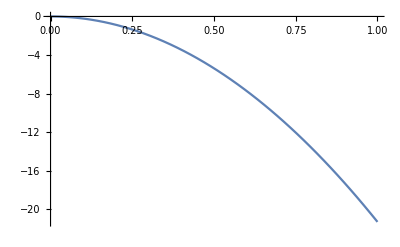

```mathematica
ReVsInter=Quiet[ReVsm0[1/100,0.2,0.17]];
Plot[ReVsInter[x/0.197],{x,0,1},PlotRange->All]
```

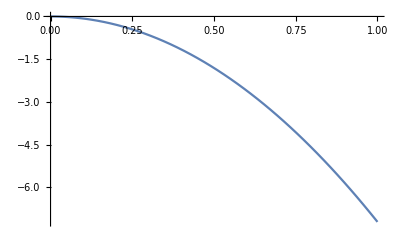

```mathematica
ReVsInter=Quiet[ImVs[1/1000,0.2,0.17]];
Plot[ReVsInter[x/0.197],{x,0,1},PlotRange->All]
```

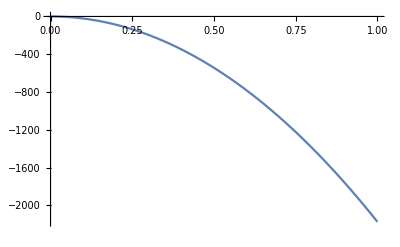

```mathematica
ReVsInter=Quiet[ReVsm0[1/10000,0.2,0.17]];
Plot[ReVsInter[x/0.197],{x,0,1},PlotRange->All]
```

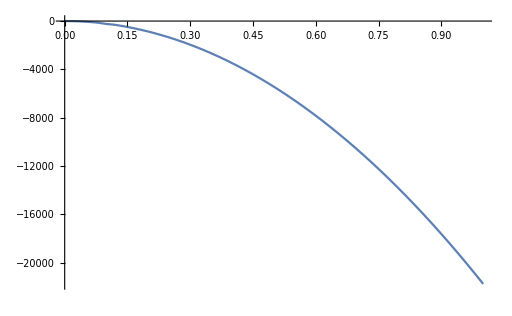

```mathematica
ReVsInter=Quiet[ReVsm0[1/100000,0.2,0.17]];
Plot[ReVsInter[x/0.197],{x,0,1},PlotRange->All]
```